```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/y/Nutstore Files/1Project/1Qdia/code/Git/Fig2

```mathematica
lossPN2 = Import["Nq2/Res/lossPv0.txt","Data"];
epochmaxN2 = 1500;
lossPN2⟦All,2⟧=lossPN2⟦All,2⟧/epochmaxN2;
lossPN2⟦All,6⟧ = lossPN2⟦All,6⟧/lossPN2⟦1,8⟧;
```

```mathematica
lossResN2=lossPN2⟦All,{2,4}⟧;
PsqureResN2 = lossPN2⟦All,{2,6}⟧;
PurityResN2 = lossPN2⟦All,{2,8}⟧;
offDResN2= lossPN2⟦All,{2,10}⟧;
```

```mathematica
lossPN3 = Import["Nq3/Res/lossPv0.txt","Data"];
epochmaxN3 = 1500;
lossPN3⟦All,2⟧=lossPN3⟦All,2⟧/epochmaxN3;
lossPN3⟦All,6⟧ = lossPN3⟦All,6⟧/lossPN3⟦1,8⟧;
lossResN3=lossPN3⟦All,{2,4}⟧;
PsqureResN3 = lossPN3⟦All,{2,6}⟧;
PurityResN3 = lossPN3⟦All,{2,8}⟧;
offDResN3= lossPN3⟦All,{2,10}⟧;
```

```mathematica
lossPN4 = Import["Nq4/Res/lossPv0.txt","Data"];
epochmaxN4= 1500;
lossPN4⟦All,2⟧=lossPN4⟦All,2⟧/epochmaxN4;
lossPN4⟦All,6⟧ = lossPN4⟦All,6⟧/lossPN4⟦1,8⟧;
lossResN4=lossPN4⟦All,{2,4}⟧;
PsqureResN4 = lossPN4⟦All,{2,6}⟧;
PurityResN4 = lossPN4⟦All,{2,8}⟧;
offDResN4= lossPN4⟦All,{2,10}⟧;
```

```mathematica
lossPN5 = Import["Nq5/Res/lossPv0.txt","Data"];
epochmaxN5= 1500;
lossPN5⟦All,2⟧=lossPN5⟦All,2⟧/epochmaxN5;
lossPN5⟦All,6⟧ = lossPN5⟦All,6⟧/lossPN5⟦1,8⟧;
lossResN5=lossPN5⟦All,{2,4}⟧;
PsqureResN5 = lossPN5⟦All,{2,6}⟧;
PurityResN5 = lossPN5⟦All,{2,8}⟧;
offDResN5= lossPN5⟦All,{2,10}⟧;
```

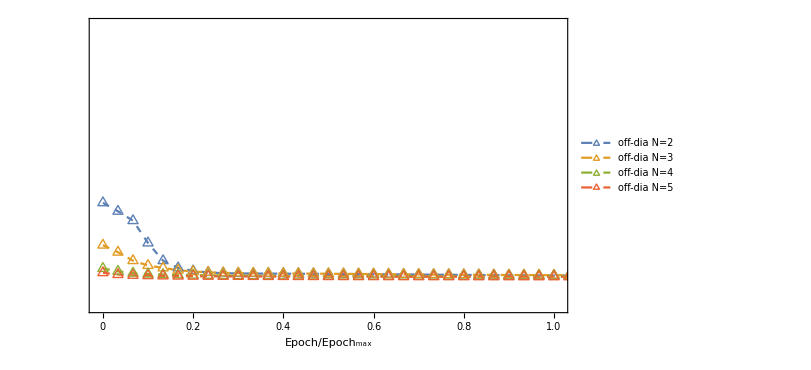

```mathematica
FigoffD=ListLinePlot[{offDResN2,offDResN3,offDResN4,offDResN5},PlotRange->{{-0.01,1.01},{-0.02,0.17}},
PlotStyle->{Dashed},
FrameLabel->{{None,Style["(|SubscriptBox[ρ, off - dia]|)^(—————–)",Italic,Directive[Large],Black,FontSize->20]},{Style["Epoch/Epoch_max",Black,Directive[Large],FontSize->20],None}},RotateLabel->True,
GridLines->{{},{}},GridLinesStyle->Directive[Red,Dashed,Thickness[0.005]],
Frame->True,Axes->None,FrameStyle->Thick,FrameTicksStyle->Directive[Black,Bold,16],PlotMarkers->{Style["△",FontSize->12]},
FrameTicks->{{None,{{0,"0.0"},0.05,{0.1,"0.10"},0.30,0.15,0.4,0.6,0.8,{1.0,"1.0"}}},{{0,0.2,0.4,0.6,0.8,{1.0,"1.0"}},None}},
PlotLegends->Placed[{Style["off-dia N=2",Bold,FontSize->14],Style["off-dia N=3",Bold,FontSize->14],Style["off-dia N=4",Bold,FontSize->14],Style["off-dia N=5",Bold,FontSize->14]},{0.75,0.505}],
ImageSize->{600,400},ImagePadding->{{80,80},{60,60}}]
```

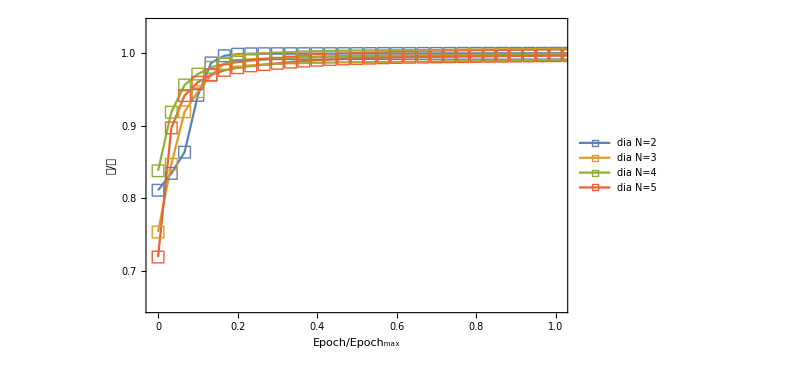

```mathematica
FigDia=ListLinePlot[{PsqureResN2,PsqureResN3,PsqureResN4,PsqureResN5},PlotRange->{{-0.01,1.01},{0.65,1.04}},FrameLabel->{{Style["𝒟/𝒫",Italic,Directive[Large],Black,FontSize->20],None},{Style["Epoch/Epoch_max",Black,Directive[Large],FontSize->20],None}},RotateLabel->True,
Frame->True,Axes->None,FrameStyle->Thick,FrameTicksStyle->Directive[Black,Bold,16],PlotMarkers->{Style["□",FontSize->12]},
FrameTicks->{{{{0,"0.0"},0.1,0.2,0.4,0.6,0.8,0.7,0.9,{1.0,"1.0"}},None},{{0,0.2,0.4,0.6,0.8,{1.0,"1.0"}},None}},
PlotLegends->Placed[{Style["dia N=2",Bold,FontSize->14],Style["dia N=3",Bold,FontSize->14],Style["dia N=4",Bold,FontSize->14],Style["dia N=5",Bold,FontSize->14]},{0.48,0.5}],
ImageSize->{600,400},ImagePadding->{{80,80},{60,60}}]
```

```mathematica
FigTrain=Overlay[{FigDia,FigoffD}]
```

-Graphics--Graphics-

```mathematica
Export["./Fig2.pdf",FigTrain]
```

./Fig1.pdf